```mathematica
(*Poisson Bracket*)
PBIϕ[F_,G_]:=D[F,ϕ1]D[G,I1]-D[F,I1]D[G,ϕ1]+D[F,ϕ2]D[G,I2]-D[F,I2]D[G,ϕ2]+D[F,ϕ3]D[G,I3]-D[F,I3]D[G,ϕ3]+D[F,ϕ4]D[G,I4]-D[F,I4]D[G,ϕ4]
```

```mathematica
(*Stuff to compute the action-angle coordinates, invariants of the S^1-action*)
```

```mathematica
Rj=I3;
N1j=I1+I2+2*I3;
N2j=I3+I4;
Kj=I2+I3;
Xj:=Sqrt[16I1*I2*I3*I4]*Cos[ϕ1+ϕ2-ϕ3+ϕ4];
Yj:=Sqrt[16I1*I2*I3*I4]*Sin[ϕ1+ϕ2-ϕ3+ϕ4];
```

```mathematica
Simplify[(N2j-Rj)*(Kj-Rj)*Rj*(N1j-Kj-Rj)]
```

I1 I2 I3 I4

```mathematica
Isol=Solve[{R==I3,N1==I1+I2+2I3,N2==I3+I4,K==I2+I3},{I1,I2,I3,I4}][[1]]
```

{I1→-K+N1-R,I2→K-R,I3→R,I4→N2-R}

```mathematica
Simplify[Xj^2+Yj^2]
```

16 I1 I2 I3 I4

```mathematica
f[R_,j_]:=(1-R)(j-R)*R*(3-j-R);
```

```mathematica
rP=X^2-16*(N2j-Rj)*(Kj-Rj)*Rj*(N1j-Kj-Rj);
```

```mathematica
Hr[d_,b_,c_]:=d*R+1/Sqrt[2]*X+b*R^2+c*R^3
```

```mathematica
rX=Expand[SolveValues[Hr[d,b,c]==h,X]][[1]]
```

√2 h-√2 d R-√2 b R^2-√2 c R^3

```mathematica
rP11=rP/.X->rX
```

-16 I1 I2 I3 I4+(√2 h-√2 d R-√2 b R^2-√2 c R^3)^2

```mathematica
rP1=rP11/.{I2->(K-R),I3->R,I1->N1-K-R,I4->N2-R}
```

-16 (K-R) (-K+N1-R) (N2-R) R+(√2 h-√2 d R-√2 b R^2-√2 c R^3)^2

```mathematica
(*Hamiltonian flow stuff*)
Hj[d_,b_,c_]:=d*Rj+1/Sqrt[2]*Xj+b*Rj^2+c*Rj^3
```

```mathematica
vfHj=Table[FullSimplify[PBIϕ[v,Hj[d,b,c]],I1>0&&I2>0&&I3>0&&I4>0],{v,{ϕ1,ϕ2,ϕ3,ϕ4,I1,I2,I3,I4}}]
```

{√2 √((I2 I3 I4)/I1) Cos[ϕ1+ϕ2-ϕ3+ϕ4],√2 √((I1 I3 I4)/I2) Cos[ϕ1+ϕ2-ϕ3+ϕ4],d+I3 (2 b+3 c I3)+√2 √((I1 I2 I4)/I3) Cos[ϕ1+ϕ2-ϕ3+ϕ4],√2 √((I1 I2 I3)/I4) Cos[ϕ1+ϕ2-ϕ3+ϕ4],2 √2 √(I1 I2 I3 I4) Sin[ϕ1+ϕ2-ϕ3+ϕ4],2 √2 √(I1 I2 I3 I4) Sin[ϕ1+ϕ2-ϕ3+ϕ4],-2 √2 √(I1 I2 I3 I4) Sin[ϕ1+ϕ2-ϕ3+ϕ4],2 √2 √(I1 I2 I3 I4) Sin[ϕ1+ϕ2-ϕ3+ϕ4]}

```mathematica
addt={ϕ1->ϕ1[t],ϕ2->ϕ2[t],ϕ3->ϕ3[t],ϕ4->ϕ4[t],I1->I1[t],I2->I2[t],I3->I3[t],I4->I4[t]};
eqsHj=MapThread[Equal,{
{ϕ1'[t],ϕ2'[t],ϕ3'[t],ϕ4'[t],I1'[t],I2'[t],I3'[t],I4'[t]},
vfHj/.addt
}]
```

{ϕ1'[t]==√2 Cos[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]] √((I2[t] I3[t] I4[t])/I1[t]),ϕ2'[t]==√2 Cos[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]] √((I1[t] I3[t] I4[t])/I2[t]),ϕ3'[t]==d+I3[t] (2 b+3 c I3[t])+√2 Cos[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]] √((I1[t] I2[t] I4[t])/I3[t]),ϕ4'[t]==√2 Cos[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]] √((I1[t] I2[t] I3[t])/I4[t]),I1'[t]==2 √2 √(I1[t] I2[t] I3[t] I4[t]) Sin[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]],I2'[t]==2 √2 √(I1[t] I2[t] I3[t] I4[t]) Sin[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]],I3'[t]==-2 √2 √(I1[t] I2[t] I3[t] I4[t]) Sin[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]],I4'[t]==2 √2 √(I1[t] I2[t] I3[t] I4[t]) Sin[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]]}

```mathematica
(*Initial conditions*)
Ydot=Simplify[PBIϕ[Yj,Hj[d,b,c]]]
```

4 √2 (I1 I2 (I3-I4)+I1 I3 I4+I2 I3 I4)-4 (d+I3 (2 b+3 c I3)) √(I1 I2 I3 I4) Cos[ϕ1+ϕ2-ϕ3+ϕ4]

```mathematica
init[Kv_,hv_,N1v_,N2v_,dv_,bv_,cv_]:=Module[{Rsol,Xsol,Rv,Xv,Ydotv,ϕ1v,ϕ2v,ϕ3v,ϕ4v,I1v,I2v,I3v,I4v},
Rsol=Sort[
NSolveValues[(0==rP1/.{K->Kv,N1->N1v,N2->N2v,h->hv,R->Rv,I3->Rv,I2->(N1v-Kv-Rv),I1->N1v-Kv-Rv,I4->(N2v-Rv),d->dv,b->bv,c->cv})&&0<=Rv<=Min[Kv,N2v,N1v-Kv],Rv]];
DeleteMissing[Table[
Xv=(rX/.{h->hv,K->Kv,R->Rv,N1->N1v,N2->N2v,I3->Rv,I4->(N2v-Rv),d->dv,b->bv,c->cv});
I1v=N1v-Kv-Rv;
I2v=Kv-Rv;
I3v=Rv;
I4v=N2v-Rv;
ϕ1v=0;
ϕ2v=0;
ϕ3v=If[Xv>=0,0,Pi];
ϕ4v=0;
Ydotv=(Ydot/.{I1->I1v,I2->I2v,I3->I3v,I4->I4v,ϕ1->ϕ1v,ϕ2->ϕ2v,ϕ3->ϕ3v,ϕ4->ϕ4v,d->dv,b->bv,c->cv});
If[Ydotv>0,{ϕ1v,ϕ2v,ϕ3v,ϕ4v,I1v,I2v,I3v,I4v},Missing[]]
,{Rv,Rsol}]]
]
```

```mathematica
(*Get the bifurcation diagrams of the systems*)
rDP1=FullSimplify[D[rP1,R]]
```

4 (-d h+4 K (K-N1) N2+(d^2-2 b h-8 K^2+8 K N1+8 N1 N2) R+3 (b d-c h-4 (N1+N2)) R^2+2 (8+b^2+2 c d) R^3+5 b c R^4+3 c^2 R^5)

```mathematica
rP1
```

-16 (K-R) (-K+N1-R) (N2-R) R+(√2 h-√2 d R-√2 b R^2-√2 c R^3)^2

```mathematica
rDDP1=FullSimplify[D[rDP1,R]]
```

4 (d^2-2 b h-8 K^2+8 K N1+8 N1 N2+6 d R (b+2 c R)+R (-6 c h-24 (N1+N2)+6 (8+b^2) R+5 c R^2 (4 b+3 c R)))

```mathematica
roughBD1[Kv_,N1v_,N2v_,dv_,bv_,cv_]:=Module[{hv,Rv,p,dp,hsol},
p=(rP1/.{K->Kv,h->hv,R->Rv,N1->N1v,N2->N2v,b->bv,c->cv,d->dv});
dp=(rDP1/.{K->Kv,h->hv,R->Rv,N1->N1v,N2->N2v,d->dv,b->bv,c->cv});
hsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,N2v,N1v-Kv],{hv,Rv}][[All,1]];
Table[{Kv,hv},{hv,hsol}]
]
```

```mathematica
Rvaluesbifurcation[Kv_,dv_,bv_,cv_]:=Module[{hv,Rv,p,dp,Rsol},
p=(rP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,b->bv,c->cv,d->dv});
dp=(rDP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,d->dv,b->bv,c->cv});
Rsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,1,3-Kv],{hv,Rv}][[All,2]];
Table[Rv,{Rv,Rsol}]
]
```

```mathematica
roughBD1[1,3,1,100,-200,110]
```

{{1,16.6134},{1,13.8223},{1,10.},{1,10.},{1,8.41716},{1,7.63012},{1,-0.039992}}

```mathematica
Rvaluesbifurcation[1.2,100,-200,110]
```

{0.350084,0.355278,0.99964,0.875969,0.842815,0.000432155}

```mathematica
f[Rvaluesbifurcation[1.2,100,-200,110][[2]],1]
```

0.242888

```mathematica
D2X=FullSimplify[D[D[Sqrt[(N2-R)*(j-R)*R*(N1-j-R)],R],R]]
```

(-j^2 (j-N1)^2 N2^2-6 j (j-N1) N2 (N1+N2) R^2+4 (-N1 N2 (N1+N2)+j^2 (N1+5 N2)-j N1 (N1+5 N2)) R^3+3 (-4 j^2+4 j N1+N1^2+6 N1 N2+N2^2) R^4-12 (N1+N2) R^5+8 R^6)/(4 ((j-R) R (j-N1+R) (-N2+R))^(3/2))

```mathematica
(*Using the most obivous coordinate chart that I can think of for the point, which we checked that the function f is actually not null in a neighborhood of it*)
```

```mathematica
classf[Kv_,N1v_,N2v_,dv_,bv_,cv_,Rv_,hv_]:=Module[{M,m11,m22,X,p,dp,hsol,Rsol,dim,m,A,sign},
p=(rP1/.{K->Kv,h->hv,R->Rv,N1->N1v,N2->N2v,b->bv,c->cv,d->dv});
dp=(rDP1/.{K->Kv,h->hv,R->Rv,N1->N1v,N2->N2v,d->dv,b->bv,c->cv});
dim=Length[hsol];
sign[RR_,hh_]:=If[(rX/.{h->hh,K->Kv,R->RR,N1->N1v,N2->N2v,I3->RR,I4->(N2v-RR),d->dv,b->bv,c->cv})>0,1,-1];
Eigenvalues[{{2*bv+6*cv*Rv+8/Sqrt[2]*sign[Rv,hv]*D2X/.{j->Kv,N1->N1v,N2->N2v,R->Rv},0},{0,-1/Sqrt[2]*rX/.{h->hv,K->Kv,R->Rv,N1->N1v,N2->N2v,I3->Rv,I4->(N2v-Rv),d->dv,b->bv,c->cv}}}]
]
```

```mathematica
classf[1.2,3,1,100,-200,110,Rvaluesbifurcation[1.2,100,-200,110][[2]],roughBD1[1.2,3,1,100,-200,110][[2,2]]]
```

{-147.539,1.49542}

```mathematica
(*And so the index is 1*)
```

```mathematica
classfcase3[Kv_]:=Module[{M,m11,m22,X,Rv,hv,p,dp,hsol,Rsol,dim,m,A,sign},
p=(rP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,b->-200,c->110,d->100});
dp=(rDP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,d->100,b->-200,c->110});
hsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,1,3-Kv],{hv,Rv}][[All,1]];
Rsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,1,3-Kv],{hv,Rv}][[All,2]];
dim=Length[hsol];
Table[Which[dim==4&&i==2,1,dim<4,0,dim==6&&i==2,1,dim==6&&i==4,1,dim==6&&i==1,0,dim==6&&i==3,0,dim==6&&i==5,0,dim==6&&i==6,0,dim>4&&i==7,0,dim==4&&i==1,0,dim==4&&i==3,0,dim==4&&i==4,0,
dim==7&&i==1,0,dim==7&&i==2,1,dim==7&&i==3,0,dim==7&&i==4,0,dim==7&&i==5,1,dim==7&&i==6,0,dim==7&&i==7,0],{i,1,dim}]
]
```

```mathematica
classfcase1[Kv_]:=Module[{M,m11,m22,X,Rv,hv,p,dp,hsol,Rsol,dim,m,A,sign},
p=(rP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,b->-35,c->17,d->20});
dp=(rDP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,d->20,b->-35,c->17});
hsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,1,3-Kv],{hv,Rv}][[All,1]];
Rsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,1,3-Kv],{hv,Rv}][[All,2]];
dim=Length[hsol];
Table[Which[dim==4&&i==1,0,dim==4&&i==3,0,dim==4&&i==4,0,dim==4&&i==2,1,dim<4,0,dim==6&&i==2,1,dim==6&&i==4,0,dim==6&&i==1,0,dim==6&&i==3,0,dim==6&&i==5,0,dim==6&&i==6,0,dim>4&&i==7,0],{i,1,dim}]
]
```

```mathematica
classfcase2[Kv_]:=Module[{M,m11,m22,X,Rv,hv,p,dp,hsol,Rsol,dim,m,A,sign},
p=(rP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,b->-35/Sqrt[2],c->17/Sqrt[2],d->20/Sqrt[2]});
dp=(rDP1/.{K->Kv,h->hv,R->Rv,N1->3,N2->1,d->20/Sqrt[2],b->-35/Sqrt[2],c->17/Sqrt[2]});
hsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,1,3-Kv],{hv,Rv}][[All,1]];
Rsol=NSolveValues[p==0&&dp==0&&0<=Rv<=Min[Kv,1,3-Kv],{hv,Rv}][[All,2]];
dim=Length[hsol];
Table[Which[dim==4&&i==1,0,dim==4&&i==3,0,dim==4&&i==4,0,dim==4&&i==2,1,dim<4,0,dim==6&&i==2,0,dim==6&&i==4,1,dim==6&&i==1,0,dim==6&&i==3,0,dim==6&&i==5,0,dim==6&&i==6,0,dim>4&&i==7,0],{i,1,dim}]
]
```

```mathematica
hyperboliclinecase3K[Kv_]:=Module[{cl,bd,dim},
cl=classfcase3[Kv];
bd=roughBD1[Kv,3,1,100,-200,110];
dim=Length[bd];
DeleteMissing[Table[If[cl[[i]]==1,{Kv,bd[[i,2]]},Missing[]],{i,1,dim}]]
]
```

```mathematica
hyperboliclinecase1K[Kv_]:=Module[{cl,bd,dim},
cl=classfcase1[Kv];
bd=ReverseSort[roughBD1[Kv,3,1,20,-35,17]];
dim=Length[bd];
DeleteMissing[Table[If[cl[[i]]==1,{Kv,bd[[i,2]]},Missing[]],{i,1,dim}]]
]
```

```mathematica
hyperboliclinecase2K[Kv_]:=Module[{cl,bd,dim},
cl=classfcase2[Kv];
bd=ReverseSort[roughBD1[Kv,3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]]];
dim=Length[bd];
DeleteMissing[Table[If[cl[[i]]==1,{Kv,bd[[i,2]]},Missing[]],{i,1,dim}]]
]
```

```mathematica
roughhyperboliclinecase3=DeleteCases[Table[hyperboliclinecase3K[Kv],{Kv,0,3,0.005}],{}];
```

```mathematica
roughhyperboliclinecase1=DeleteCases[Table[hyperboliclinecase1K[Kv],{Kv,0,3,0.005}],{}];
```

```mathematica
roughhyperboliclinecase2=DeleteCases[Table[hyperboliclinecase2K[Kv],{Kv,0,3,0.005}],{}];
```

```mathematica
parabolicvaluescase1:=Module[{list,d},
list=roughhyperboliclinecase1;
d=Length[list];
Join[list[[1]],list[[d]]]
]
```

```mathematica
parabolicvaluescase2:=Module[{list,d},
list=roughhyperboliclinecase2;
d=Length[list];
Join[list[[1]],list[[d]]]
]
```

```mathematica
parabolicvaluescase3:=Module[{list1,list2,d1,d2},
list1=Flatten[roughhyperboliclinecase3,1];
d1=Length[list1];
list2=Flatten[Table[If[list1[[i]][[2]]<10,{list1[[i]][[1]],list1[[i]][[2]]},{}],{i,1,d1}]];
d2=Length[list2];
{list1[[1]],list1[[d1]],{list2[[1]],list2[[2]]},{list2[[d2-1]],list2[[d2]]}}
]
```

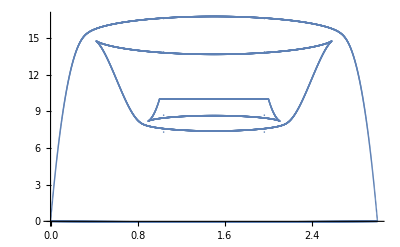

```mathematica
roughBD=Flatten[Table[roughBD1[Kv,3,1,100,-200,110],{Kv,0,3,0.001}],1];
roughBDplot=ListPlot[roughBD]
```

```mathematica
(*The way I figure out the hyperbolic-regular line is literally compute it for some points using a nice enough coordinate chart and then the result follows for the whole line and I did that manually, maybe there is a better way .... *)
```

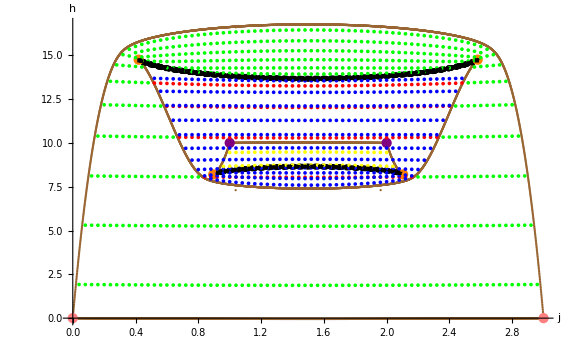

```mathematica
rank0pointsinside[dv_,bv_,cv_]:={{1,dv+bv+cv},{2,dv+bv+cv}}
rank0pointboundary:={{0,0},{3,0}};
Show[ListPlot[roughBD,PlotStyle->Brown],ListPlot[rank0pointsinside[100,-200,110],ImageSize->Large,PlotStyle->Purple],ListPlot[roughhyperboliclinecase3,ImageSize->Large,PlotStyle->Black,PlotMarkers->{Automatic,4}],ListPlot[parabolicvaluescase3,PlotStyle->Orange],ListPlot[rank0pointboundary,ImageSize->Large,PlotStyle->Pink],ListPlot[{newspec0,newspec1,newspec2,newspec3},PlotStyle->{Green,Red,Blue,Yellow}],ImageSize->Large,AxesLabel->{j,h}]
```

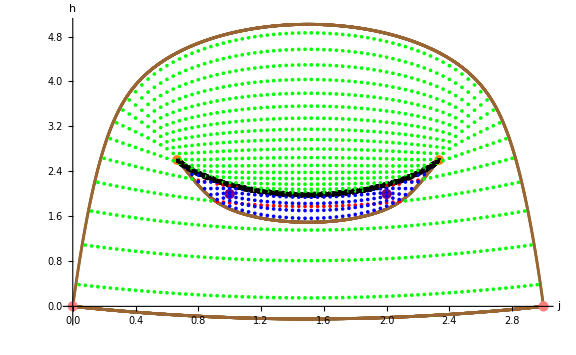

```mathematica
Show[ListPlot[Flatten[Table[roughBD1[Kv,3,1,20,-35,17],{Kv,0,3,0.001}],1],PlotStyle->Brown],ListPlot[rank0pointsinside[20,-35,17],ImageSize->Large,PlotStyle->Purple],ListPlot[roughhyperboliclinecase1,ImageSize->Large,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],ListPlot[parabolicvaluescase1,PlotStyle->Orange,PlotMarkers->{Automatic,10}],ListPlot[rank0pointboundary,ImageSize->Large,PlotStyle->Pink],ListPlot[{nnewspec0,nnewspec1,nnewspec2},ImageSize->Large,PlotStyle->{Green,Red,Blue}],ImageSize->Large,AxesLabel->{j,h}]
```

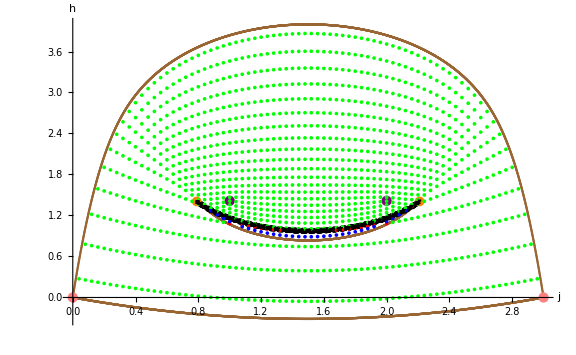

```mathematica
Show[ListPlot[Flatten[Table[roughBD1[Kv,3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],{Kv,0,3,0.001}],1],PlotStyle->Brown],ListPlot[rank0pointsinside[20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],ImageSize->Large,PlotStyle->Purple],ListPlot[roughhyperboliclinecase2,ImageSize->Large,PlotStyle->Black,PlotMarkers->{Automatic,Tiny}],ListPlot[parabolicvaluescase2,PlotStyle->Orange,PlotMarkers->{Automatic,10}],ListPlot[rank0pointboundary,ImageSize->Large,PlotStyle->Pink],ListPlot[{nnnewspec0,nnnewspec1,nnnewspec2},ImageSize->Large,PlotStyle->{Green,Red,Blue}],
ImageSize->Large,AxesLabel->{j,h}]
```

```mathematica
(*Compute action*)
computeAction[initv_,dv_,bv_,cv_]:=Module[
{act,actv,ϕ1v,ϕ2v,ϕ3v,ϕ4v,Kv,N1v,N2v,T},
Kv=initv[[6]]+initv[[7]]; (* K=I2+I3 *)
N1v=initv[[5]]+initv[[6]]+2initv[[7]]; (* N1=I1+I2+2I3 *)
N2v=initv[[7]]+initv[[8]]; (* N2=I3+I4 *)
{actv,ϕ1v,ϕ2v,ϕ3v,ϕ4v}=NDSolveValue[{
(eqsHj/.{d->dv,b->bv,c->cv}),
MapThread[Equal,{
{ϕ1[0],ϕ2[0],ϕ3[0],ϕ4[0],I1[0],I2[0],I3[0],I4[0]},
initv
}],
{act'[t]==I1[t]ϕ1'[t]+I2[t]ϕ2'[t]+I3[t]ϕ3'[t]+I4[t]ϕ4'[t],act[0]==0},
WhenEvent[Sin[ϕ1[t]+ϕ2[t]-ϕ3[t]+ϕ4[t]]>0,T=t;If[t>10^-10,"StopIntegration"]]},
{act[T],ϕ1[T],ϕ2[T],ϕ3[T],ϕ4[T]},
{t,0,Infinity}];
(actv-N1v ϕ1v-N2v ϕ4v-Kv(ϕ2v-ϕ1v))/(2Pi)
]
```

```mathematica
init[1,0.5,3,1,20,-35,17][[1]]
```

{0,0,π,0,1.90602,0.90602,0.0939804,0.90602}

```mathematica
init[1.5,9,3,1,100,-200,110]
```

{{0,0,π,0,1.36099,1.36099,0.13901,0.86099},{0,0,0,0,0.689592,0.689592,0.810408,0.189592},{0,0,π,0,0.528475,0.528475,0.971525,0.0284751}}

```mathematica
{computeAction[init[1.5,1.5,3,1,20,-35,17][[1]],20,-35,17],computeAction[init[1.5,1.5,3,1,20,-35,17][[2]],20,-35,17]}
```

{0.112123,0.00120388}

```mathematica
(*Joint spectrum stuff*)
clN[invhbar_]:=Module[{M1,M2,N1,N2},
M1=3invhbar-2;
M2=invhbar-1;
N1=(M1+2)/invhbar;
N2=(M2+1)/invhbar;
{M1,M2,N1,N2}]
```

```mathematica
clN[25]
```

{73,24,3,1}

```mathematica
Rop[k_,invhbar_]:=Module[{m1,m2,N1,N2,mmax,m},
{m1,m2,N1,N2}=clN[invhbar];
mmax=Min[k,m2,m1-k];
1/invhbar DiagonalMatrix[Table[m+1/2,{m,0,mmax}]]]
```

```mathematica
Xop[k_,invhbar_]:=Module[{m1,m2,N1,N2,mmax,m,n1,n2,n3,n4,op},
{m1,m2,N1,N2}=clN[invhbar];
mmax=Min[k,m2,m1-k];
op=Table[0,mmax+1,mmax+1];
n1=m1-k-m;
n2=k-m;
n3=m;
n4=m2-m;
Do[
If[m>=1,op[[m+1,m]]=-2/invhbar^2 Sqrt[(n1+1)(n2+1)n3(n4+1)]];
If[m<=mmax-1,op[[m+1,m+2]]=-2/invhbar^2 Sqrt[n1 n2 (n3+1)n4]];
,{m,0,mmax}];
op
]
```

```mathematica
Hop[k_,invhbar_,d_,b_,c_]:=Module[{R,X},
R=Rop[k,invhbar];
X=Xop[k,invhbar];
d*R+ 1/Sqrt[2]*X+b MatrixPower[R,2]+c MatrixPower[R,3]
]
```

```mathematica
Rv[Kv_,hv_,N1v_,N2v_,dv_,bv_,cv_]:=Module[{Rsol,Xsol,Rv,Xv,Ydotv,ϕ1v,ϕ2v,ϕ3v,ϕ4v,I1v,I2v,I3v,I4v},
Rsol=Sort[
NSolveValues[(0==rP1/.{K->Kv,h->hv,N1->N1v,N2->N2v,R->Rv,d->dv,b->bv,c->cv})&&0<=Rv<=Min[Kv,N2v,N1v-Kv],Rv]];
Rsol]
```

```mathematica
Rv[1,9,3,1,100,-200,110]
```

{0.0967675,0.137085,0.695043,0.789608,0.953093,0.964768}

```mathematica
Rv[1,12,3,1,100,-200,110]
```

{0.14726,0.215971,0.531316,0.634198}

```mathematica
classify[Rexpval_,Kv_,hv_,d_,b_,c_]:=Module[{Rsol},
Rsol=Rv[Kv,hv,3,1,d,b,c];
If[Length[Rsol]==2,Return[0]];
If[Length[Rsol]==4&&Rsol[[1]]<=Rexpval<=Rsol[[2]],Return[1]];
If[Length[Rsol]==4&&Rsol[[3]]<=Rexpval<=Rsol[[4]],Return[2]];
If[Length[Rsol]==6&&Rsol[[1]]<=Rexpval<=Rsol[[2]],Return[1]];
If[Length[Rsol]==6&&Rsol[[3]]<=Rexpval<=Rsol[[4]],Return[2]];
If[Length[Rsol]==6&&Rsol[[5]]<=Rexpval<=Rsol[[6]],Return[3]];
]
```

```mathematica
spec[k_,invhbar_,d_,b_,c_]:=Module[{i,hbar,kv,hop,Rexpval,eval,evec,msize,M1,M2,N1v,N2v,jv},
hbar=1/invhbar;
hop=N[Hop[k,invhbar,d,b,c]];
{eval,evec}=Eigensystem[hop];
msize=Length[eval];
Rexpval=Table[Chop[Conjugate[Transpose[evec[[i]]].Rop[k,invhbar].evec[[i]]]],{i,1,msize}];
kv=(k+1)hbar;
Table[{N[kv],eval[[i]],Rexpval[[i]],classify[Rexpval[[i]],N[kv],eval[[i]],d,b,c]},{i,1,Length[eval]}]
]
```

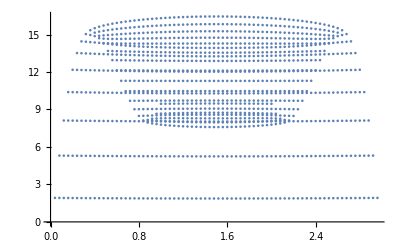

```mathematica
newspec=With[{invhbar=25},Flatten[Table[spec[k,invhbar,100,-200,110],{k,0,clN[invhbar][[1]]}],1]];
roughSPplot=ListPlot[newspec[[All,{1,2}]]]
```

```mathematica
newspec0=Select[newspec,#[[4]]==0&][[All,{1,2}]];
newspec1=Select[newspec,#[[4]]==1&][[All,{1,2}]];
newspec2=Select[newspec,#[[4]]==2&][[All,{1,2}]];
newspec3=Select[newspec,#[[4]]==3&][[All,{1,2}]];
```

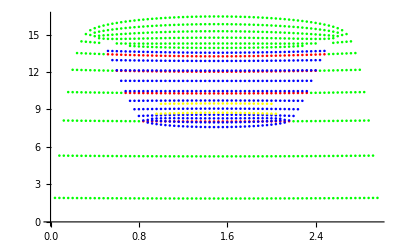

```mathematica
ListPlot[{newspec0,newspec1,newspec2,newspec3},PlotStyle->{Green,Red,Blue,Yellow}]
```

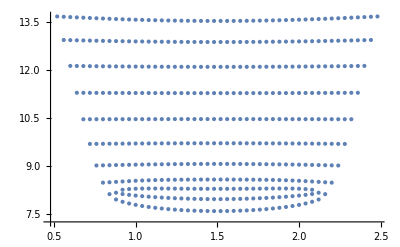

```mathematica
ListPlot[newspec2]
```

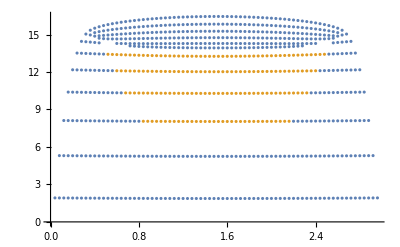

```mathematica
ListPlot[{newspec0,newspec1}]
```

```mathematica
(*Compute classical action on spectrum points in the case of the flap inside of a flap*)
```

```mathematica
actspec0=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,100,-200,110][[1]],100,-200,110],jh[[2]]},{jh,newspec0}];
```

```mathematica
actspec1=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,100,-200,110][[1]],100,-200,110],jh[[2]]},{jh,newspec1}];
```

```mathematica
actspec2=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,100,-200,110][[2]],100,-200,110],jh[[2]]},{jh,newspec2}];
```

```mathematica
actspec3=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,100,-200,110][[3]],100,-200,110],jh[[2]]},{jh,newspec3}];
```

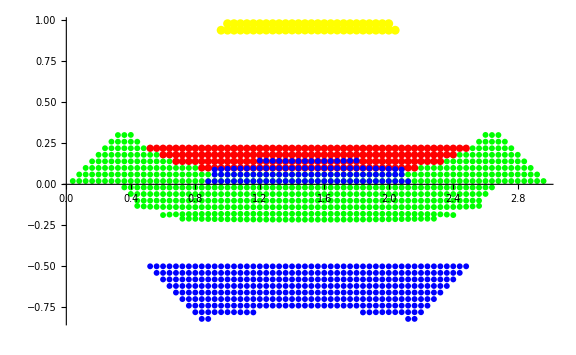

```mathematica
Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec0}],PlotStyle->Green],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec2}],PlotStyle->Blue],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec3}],PlotStyle->Yellow],
ImageSize->Large,PlotRange->All]
```

```mathematica
(*Fix the spectrum now, there is multiple stuff to fix the green and the blue.*)
```

```mathematica
actspec0x=Table[{p[[1]],If[p[[2]]<0,p[[2]]+1+If[p[[1]]<1,p[[1]]-1,0]+If[p[[1]]>2,2-p[[1]],0],p[[2]]],p[[3]]},{p,actspec0}];
```

```mathematica
actspec2x=Table[{p[[1]],If[p[[2]]<0,p[[2]]+1+If[p[[1]]<1,p[[1]]-1,0]+If[p[[1]]>2,2-p[[1]],0],p[[2]]],p[[3]]},{p,actspec2}];
```

```mathematica
alternativeactspec2x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,actspec2x}];
alternativeactspec0x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,actspec0x}];
alternativeactspec1=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,actspec1}];
alternativealternativeactspec0x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,actspec0x}];
alternativealternativeactspec1=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,actspec1}];
alternativealternativealternativeactspec0x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,actspec0x}];
alternativealternativealternativeactspec1=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,actspec1}];
alternativealternativeactspec2x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,actspec2x}];
alternativealternativealternativeactspec2x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,actspec2x}];
```

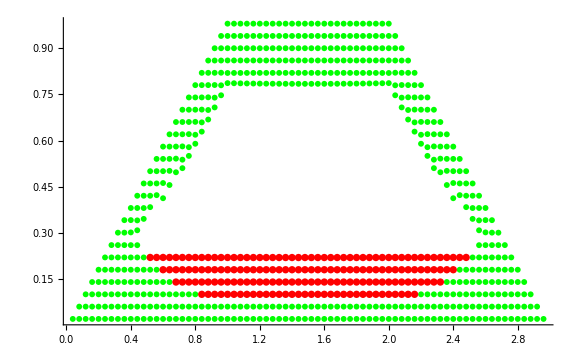

```mathematica
Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec0x}],PlotStyle->Green],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec1}],PlotStyle->Red],
ImageSize->Large,PlotRange->All]
```

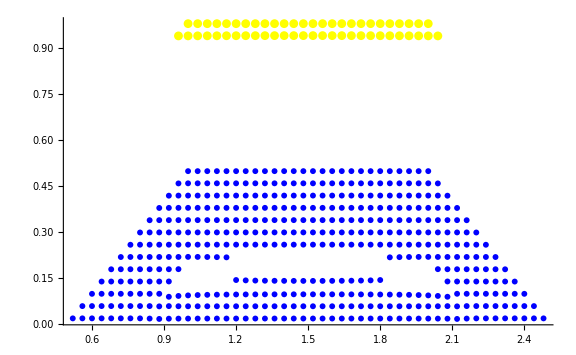

```mathematica
Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec2x}],PlotStyle->Blue],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec3}],PlotStyle->Yellow],
ImageSize->Large,PlotRange->All]
```

```mathematica
p1111:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,actspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],-1+s[[2]]},s[[3]]],{s,actspec2x}],PlotStyle->Blue],
ListPlot[Table[Tooltip[{s[[1]],(-1+s[[2]])+1.5},s[[3]]],{s,actspec3}],PlotStyle->Yellow,PlotMarkers->{Automatic,3}],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-1.1,1.6}}]
```

```mathematica
pminus11minusminusminus1:=Show[ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativeactspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativeactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],-1+s[[2]]},s[[3]]],{s,alternativeactspec2x}],PlotStyle->Blue],
ListPlot[Table[Tooltip[{s[[1]],(-1+s[[2]])+1.5},s[[3]]],{s,actspec3}],PlotStyle->Yellow,PlotMarkers->{Automatic,3}],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-1.1,1.6}}]
```

```mathematica
p1minus1minus11:=Show[ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativealternativeactspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativealternativeactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],-1+s[[2]]},s[[3]]],{s,alternativealternativeactspec2x}],PlotStyle->Blue],
ListPlot[Table[Tooltip[{s[[1]],(-1+s[[2]])+1.5},s[[3]]],{s,actspec3}],PlotStyle->Yellow,PlotMarkers->{Automatic,3}],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-1.1,1.6}}]
```

```mathematica
pminus1minus1minus11:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativeactspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativeactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],-1+s[[2]]},s[[3]]],{s,alternativealternativealternativeactspec2x}],PlotStyle->Blue],
ListPlot[Table[Tooltip[{s[[1]],(-1+s[[2]])+1.5},s[[3]]],{s,actspec3}],PlotStyle->Yellow,PlotMarkers->{Automatic,3}],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-1.1,1.6}}]
```

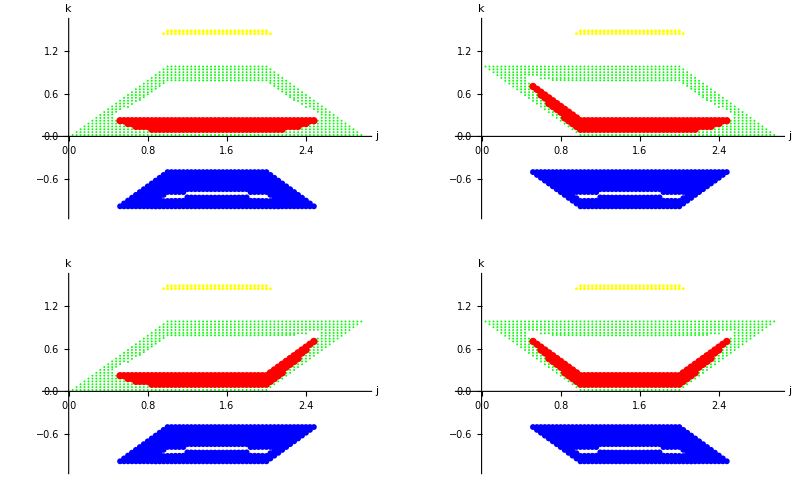

```mathematica
GraphicsGrid[{{p1111,pminus11minusminusminus1},{p1minus1minus11,pminus1minus1minus11}},Frame->All]
```

```mathematica
(*Case of focus-focus (inside inside of the flap, (d,b,c)=(20,-35,17)*)
```

```mathematica
rroughBD=Flatten[Table[roughBD1[Kv,3,1,20,-35,17],{Kv,0,3,0.005}],1];
rroughBDplot=ListPlot[rroughBD]
```

-Graphics-

```mathematica
nnewspec=With[{invhbar=25},Flatten[Table[spec[k,invhbar,20,-35,17],{k,0,clN[invhbar][[1]]}],1]];
rroughSPplot=ListPlot[nnewspec[[All,{1,2}]]];
```

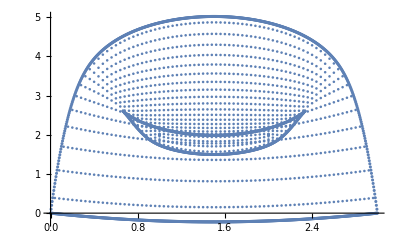

```mathematica
Show[rroughBDplot,rroughSPplot]
```

```mathematica
nnewspec0=Select[nnewspec,#[[4]]==0&][[All,{1,2}]];
nnewspec1=Select[nnewspec,#[[4]]==1&][[All,{1,2}]];
nnewspec2=Select[nnewspec,#[[4]]==2&][[All,{1,2}]];
```

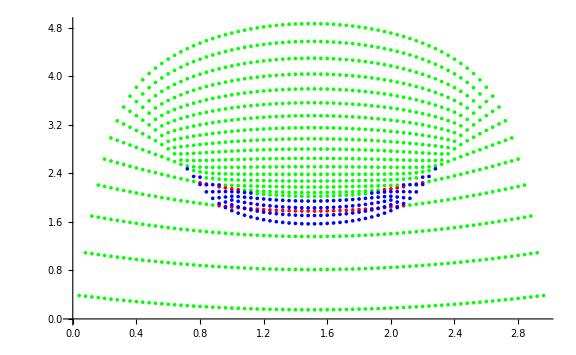

```mathematica
ListPlot[{nnewspec0,nnewspec1,nnewspec2},ImageSize->Large,PlotStyle->{Green,Red,Blue}]
```

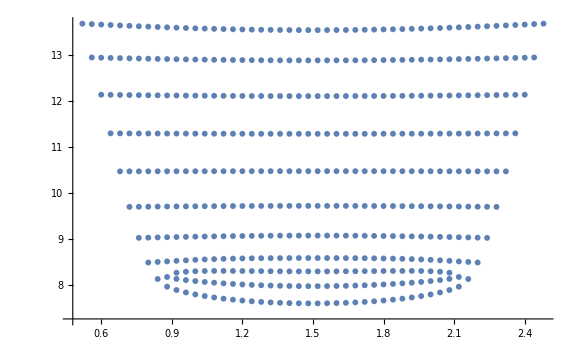

```mathematica
ListPlot[newspec2,ImageSize->Large]
```

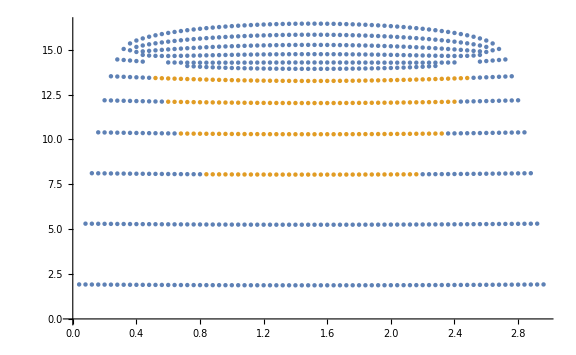

```mathematica
ListPlot[{newspec0,newspec1},ImageSize->Large]
```

```mathematica
aactspec0=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20,-35,17][[1]],20,-35,17],jh[[2]]},{jh,nnewspec0}];
```

```mathematica
aactspec1=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20,-35,17][[1]],20,-35,17],jh[[2]]},{jh,nnewspec1}];
aactspec2=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20,-35,17][[2]],20,-35,17],jh[[2]]},{jh,nnewspec2}];
```

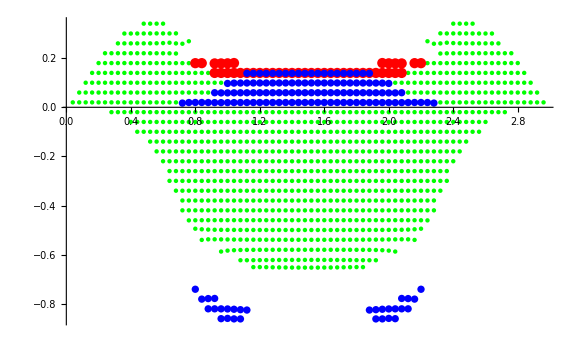

```mathematica
Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aactspec0}],PlotStyle->Green],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aactspec2}],PlotStyle->Blue],
ImageSize->Large,PlotRange->All]
```

```mathematica
aactspec0x=Table[{p[[1]],If[p[[2]]<0,p[[2]]+1+If[p[[1]]<1,p[[1]]-1,0]+If[p[[1]]>2,2-p[[1]],0],p[[2]]],p[[3]]},{p,aactspec0}];
```

```mathematica
aactspec2x=Table[{p[[1]],If[p[[2]]<0,p[[2]]+1+If[p[[1]]<1,p[[1]]-1,0]+If[p[[1]]>2,2-p[[1]],0],p[[2]]],p[[3]]},{p,aactspec2}];
```

```mathematica
aaaactspec2x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aactspec2x}];
alternativeaactspec0x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aactspec0x}];
alternativeaactspec1=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aactspec1}];
alternativealternativeaactspec0x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,aactspec0x}];
alternativealternativeaactspec1=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,aactspec1}];
alternativealternativealternativeaactspec0x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aactspec0x}];
alternativealternativealternativeaactspec1=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aactspec1}];
alternativealternativeaactspec2x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aactspec2x}];
alternativealternativealternativeaactspec2x=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,aactspec2x}];
```

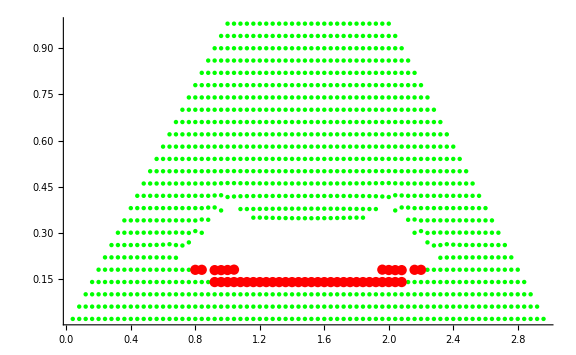

```mathematica
Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aactspec0x}],PlotStyle->Green],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aactspec1}],PlotStyle->Red],
ImageSize->Large,PlotRange->All]
```

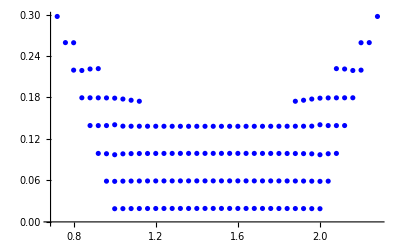

```mathematica
Show[ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aaaactspec2x}],PlotStyle->Blue]]
```

```mathematica
hminus11minusminusminus1:=Show[ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativeaactspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativeaactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.5},s[[3]]],{s,aaaactspec2x}],PlotStyle->Blue],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.6}}]
```

```mathematica
h1111:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aactspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.5},s[[3]]],{s,aactspec2x}],PlotStyle->Blue],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.6}}]
h1minus1minus11:=Show[ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativealternativeaactspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativealternativeaactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.5},s[[3]]],{s,alternativealternativeaactspec2x}],PlotStyle->Blue],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.6}}]
hminus1minus1minus11:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativeaactspec0x}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativeaactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.5},s[[3]]],{s,alternativealternativealternativeaactspec2x}],PlotStyle->Blue],
ImageSize->Large,AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.6}}]
```

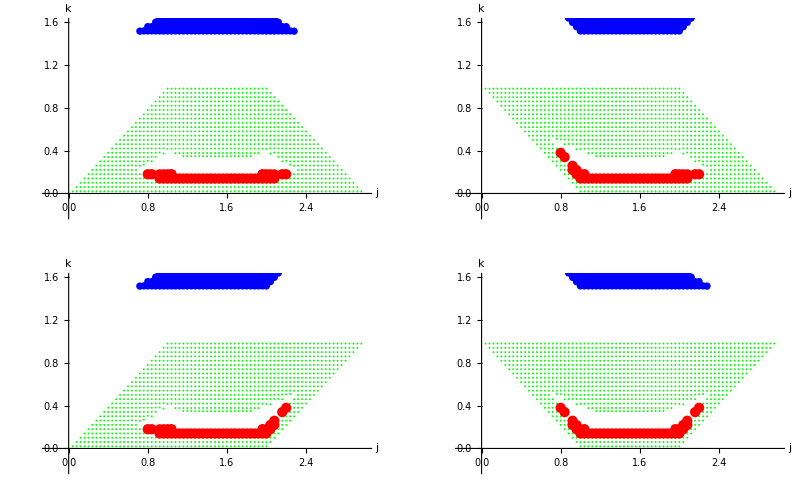

```mathematica
GraphicsGrid[{{h1111,hminus11minusminusminus1},{h1minus1minus11,hminus1minus1minus11}},Frame->All]
```

```mathematica
(*Case ff outsie of the flap (d,b,c)=1/sqrt[2](20,-35,17)*)
```

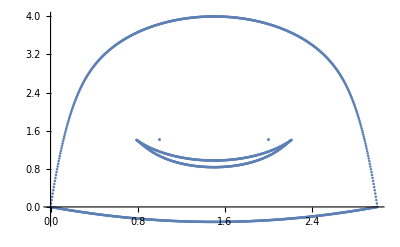

```mathematica
rrroughBD=Flatten[Table[roughBD1[Kv,3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],{Kv,0,3,0.005}],1];
rrroughBDplot=ListPlot[rrroughBD]
```

```mathematica
nnnewspec=With[{invhbar=25},Flatten[Table[spec[k,invhbar,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],{k,0,clN[invhbar][[1]]}],1]];
rrroughSPplot=ListPlot[nnnewspec[[All,{1,2}]]];
```

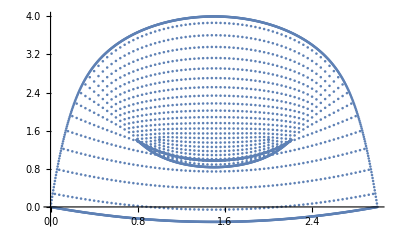

```mathematica
Show[rrroughBDplot,rrroughSPplot]
```

```mathematica
nnnewspec0=Select[nnnewspec,#[[4]]==0&][[All,{1,2}]];
nnnewspec1=Select[nnnewspec,#[[4]]==1&][[All,{1,2}]];
nnnewspec2=Select[nnnewspec,#[[4]]==2&][[All,{1,2}]];
```

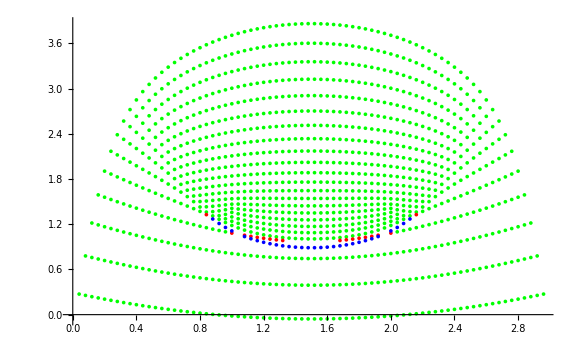

```mathematica
ListPlot[{nnnewspec0,nnnewspec1,nnnewspec2},ImageSize->Large,PlotStyle->{Green,Red,Blue}]
```

```mathematica
aaactspec0=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]][[1]],20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],jh[[2]]},{jh,nnnewspec0}];
```

```mathematica
aaactspec1=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]][[1]],20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],jh[[2]]},{jh,nnnewspec1}];
```

```mathematica
aaactspec2=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]][[2]],20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],jh[[2]]},{jh,nnnewspec2}];
```

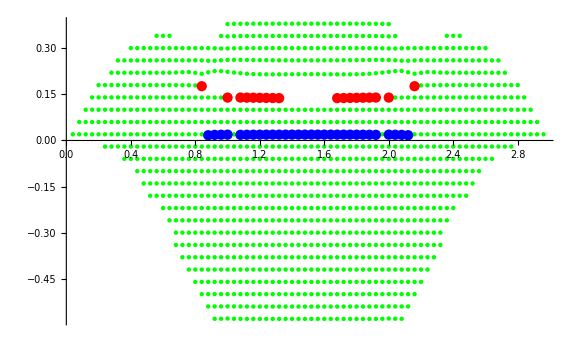

```mathematica
Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aaactspec0}],PlotStyle->Green],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aaactspec1}],PlotStyle->Red],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aaactspec2}],PlotStyle->Blue],
ImageSize->Large,PlotRange->All]
```

```mathematica
aaactspec0x=Table[{p[[1]],If[p[[2]]<0,p[[2]]+1+If[p[[1]]<1,p[[1]]-1,0]+If[p[[1]]>2,2-p[[1]],0],p[[2]]],p[[3]]},{p,aaactspec0}];
```

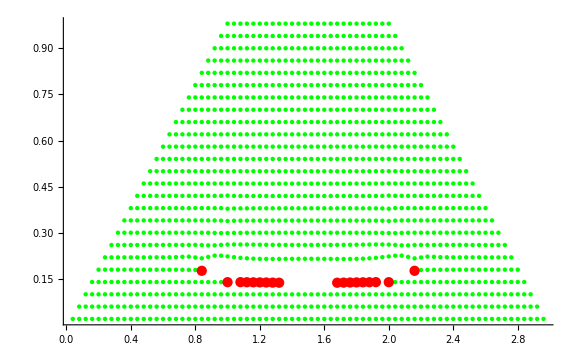

```mathematica
Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aaactspec0x}],PlotStyle->Green],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aaactspec1}],PlotStyle->Red],
ImageSize->Large,PlotRange->All]
```

```mathematica
nnnewspec50=With[{invhbar=50},Flatten[Table[spec[k,invhbar,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],{k,0,clN[invhbar][[1]]}],1]];
rrroughSPplot=ListPlot[nnnewspec[[All,{1,2}]]];
```

```mathematica
nnnewspec502=Select[nnnewspec50,#[[4]]==2&][[All,{1,2}]];
nnnewspec501=Select[nnnewspec50,#[[4]]==1&][[All,{1,2}]];
nnnewspec500=Select[nnnewspec50,#[[4]]==0&][[All,{1,2}]];
```

```mathematica
aaactspec502=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]][[2]],20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],jh[[2]]},{jh,nnnewspec502}];
```

```mathematica
aaactspec501=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]][[1]],20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],jh[[2]]},{jh,nnnewspec501}];
```

```mathematica
aaactspec500=ParallelTable[{jh[[1]],computeAction[init[jh[[1]],jh[[2]],3,1,20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]][[1]],20/Sqrt[2],-35/Sqrt[2],17/Sqrt[2]],jh[[2]]},{jh,nnnewspec500}];
```

```mathematica
fixedaactspec500=Table[{p[[1]],If[p[[2]]<0,p[[2]]+1+If[p[[1]]<1,p[[1]]-1,0]+If[p[[1]]>2,2-p[[1]],0],p[[2]]],p[[3]]},{p,aaactspec500}];
```

```mathematica
alternativefixedaactspec500=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,fixedaactspec500}];
alternativefixedaactspec501=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aaactspec501}];
alternativealternativefixedaactspec500=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,fixedaactspec500}];
alternativealternativefixedaactspec501=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,-p[[1]]+1+p[[2]],p[[1]]>2,p[[2]]],p[[3]]},{p,aaactspec501}];
alternativealternativealternativefixedaactspec500=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,fixedaactspec500}];
alternativealternativealternativefixedaactspec501=Table[{p[[1]],Which[1<=p[[1]]<=2,p[[2]],p[[1]]<1,p[[2]],p[[1]]>2,p[[1]]-2+p[[2]]],p[[3]]},{p,aaactspec501}];
```

```mathematica
g11:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,fixedaactspec500}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,aaactspec501}],PlotStyle->Red,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.2},s[[3]]],{s,aaactspec502}],PlotStyle->Blue,PlotMarkers->{Automatic,2}],AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.3}}]
```

```mathematica
gminus1minus1:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativefixedaactspec500}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativefixedaactspec501}],PlotStyle->Red,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.2},s[[3]]],{s,aaactspec502}],PlotStyle->Blue,PlotMarkers->{Automatic,2}],AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.3}}]
gminus11:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativefixedaactspec500}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativefixedaactspec501}],PlotStyle->Red,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.2},s[[3]]],{s,aaactspec502}],PlotStyle->Blue,PlotMarkers->{Automatic,2}],AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.3}}]
g1minus1:=Show[
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativealternativefixedaactspec500}],PlotStyle->Green,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]},s[[3]]],{s,alternativealternativealternativefixedaactspec501}],PlotStyle->Red,PlotMarkers->{Automatic,2}],
ListPlot[Table[Tooltip[{s[[1]],s[[2]]+1.2},s[[3]]],{s,aaactspec502}],PlotStyle->Blue,PlotMarkers->{Automatic,2}],AxesLabel->{j,k},PlotRange->{{-0.2,3},{-0.2,1.3}}]
```

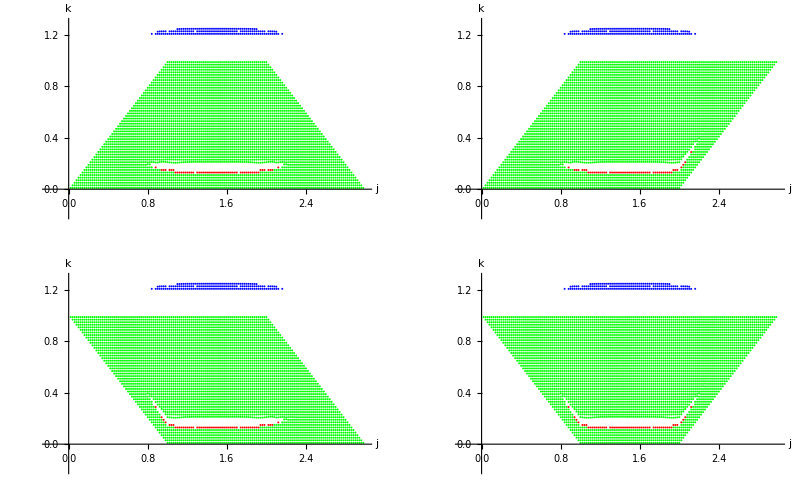

```mathematica
GraphicsGrid[{{g11,g1minus1},{gminus11,gminus1minus1}},Frame->All]
```